```mathematica
σ = 220 / Sqrt[2]
vc = 220
gd[v_,vc_,σ_]:= 2 * σ^2 * (v/vc)*Exp[-(v^2 + vc^2)/(2*σ^2)] * Sinh[v * vc / σ^2]
normalizationd= NIntegrate[gd[v,vc,σ],{v,0,100000}]
fd[v_,vc_,σ_]:= gd[v,vc,σ]/normalizationd
```

110 √2

220

9.43654×10^6

```mathematica
gh[v_,σ_]:=v^2 * Exp[-v^2 / 4 / σ^2]
normalizationh = NIntegrate[gh[v,σ],{v,0,1000000}]
fh[v_,σ_]:=gh[v,σ] / normalizationh
```

1.33453×10^7

```mathematica
Plot[{fh[v,vc,σ], fd[v,σ]},{v,0,1000}]
```

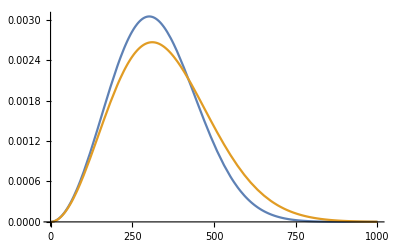

```mathematica
NIntegrate[fd[v,vc,σ],{v,0,100000}]
```

1.

```mathematica
vavgd = NIntegrate[fd[v,vc,σ] * v,{v,0,100000}]
vavgh= NIntegrate[fh[v,σ] * v,{v,0,100000}]
```

323.753

351.069

```mathematica
ΔEhh= vavgh * NIntegrate[fh[v,σ]/v^2,{v,0,100000}]
ΔEhd = 0
ΔEdh = vavgd * NIntegrate[fd[v,vc,σ]/v^2,{v,0,100000}]
ΔEdd = vavgd * (2*π )/(2*π*σ^2)^(3/2) * NIntegrate[ fd[v,vc,σ] * (1+σ^2 / v / vc),{v,0,100000}]
```

0.0072535

0

0.00719855

0.0000487643

```mathematica
ΔEh[a_,b_]:= a * ΔEhh + b * ΔEhd
ΔEd[a_,b_]:=a*ΔEdh + b*ΔEdd
```

```mathematica
G = 4.3 * 10^(-3)
a[M_,p_]:=(2*G*M  /p)^2
b[M_,p_]:= (2*G*M  /p)
```

0.0043

1

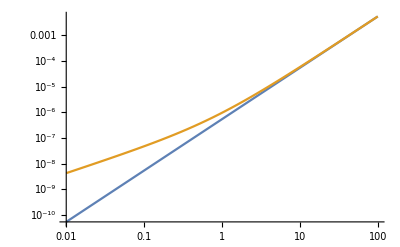

```mathematica
p =1
LogLogPlot[{ΔEh[a[M,p],b[M,p]],ΔEd[a[M,p],b[M,p]]}, {M,0.01,100}]
```